### Other stuff that needs to be updated

```mathematica
progress =Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
Length/@ progress
```

{1,4,5,2,4,2,1,3,3,1,2,3,1,1,4,1,2,1,2,3,2,3,2,4,2,1,3,1,1}

```mathematica
Length/@progress2
```

{2,5,5,2,4,2,2,3,3,1,2,3,1,1,5,1,2,1,2,3,2,4,2,4,2,1,3,1,1}

```mathematica
progress2[[All, 1]] ===progress[[All, 1]]
```

False

```mathematica
progress2[[All, 1, "Year"]] === progress[[All, 1, "Year"]]
```

True

```mathematica
progress[[All, 1, "Year"]]
```

{1969,1970,1970,1971,1972,1972,1970,1972,1983,1977,1972,1976,1970,1970,1983,1997,1995,2023,1995,1995,1997,2019,1994,1994,1983,2002,1973,1980,1970}

```mathematica
progress2 =Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

As of 1980, many periods were missing.  But in fact all periods are possible---though it wasn’t until 2023 that they were all filled in:

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, 1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, 1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

Finding an oscillator of a given period is one thing.  But how about the smallest oscillator of that period?  We can be fairly certain that not all of these are known, even for periods below 30.  But here’s a plot that shows when the progressive “smallest so far” oscillators were found for a given period:

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

And here’s the corresponding plot for all periods up to 100:

Try to get to 100

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 60}]];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 60}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

```mathematica
progress2 =DeleteCases[Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress2, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress2[[All, -1]]}), PlotRange->{{1969, 2021}, {0, 82}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

But what about the actual reduction in size that’s achieved?  Here’s a plot for each oscillator period showing the sequence of sizes found---in effect the “engineering optimization” that’s achieved:

We actually don’t need ot update these because they’re all the same anyway: if you still want to put in:

```mathematica
progress =Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

### New Names plot

Can’t figure out how to center text... this isn’t terrible

```mathematica
(*See GoL-10-Data* for retrieval code*) 
namesdiscoverers = Select[, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, "Discovered by"]];
```

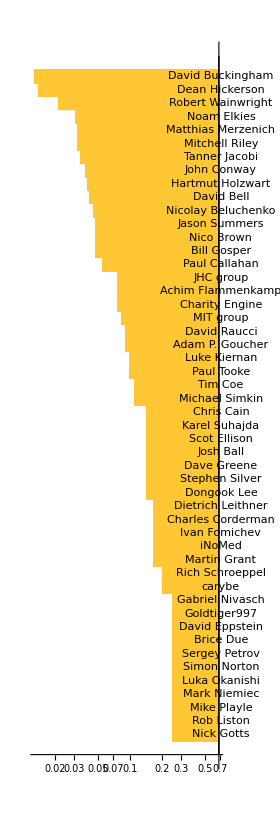
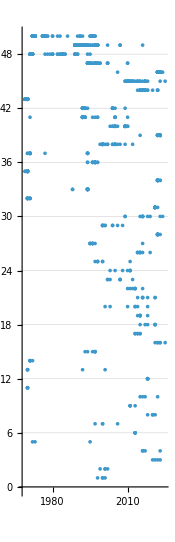

```mathematica
Row[{BarChart[Take[Sort[Counts[namesdiscoverers]],-50], BarOrigin->Right, ScalingFunctions->"Log", AspectRatio->3, ImageSize->280, PlotRangePadding->{Automatic, .8}, ChartLabels->(Style[Text[#],TextAlignment->Center]&)/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]]], ListPlot[{ToExpression[#1],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[Reverse@{First[#2], #1}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&],  AspectRatio->3.1, ImageSize->175,PlotRangePadding->{Automatic, {None, 1.8}}, PlotStyle-> PointSize[.015](*, Frame-> {False, False, True, False}, FrameTicks->Range[1969, 2025]*), Axes->{True, False}, GridLines->{None, Range[.5, 50.5, 1]}]}, Alignment->Top]
```

### Progressive

```mathematica
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
```

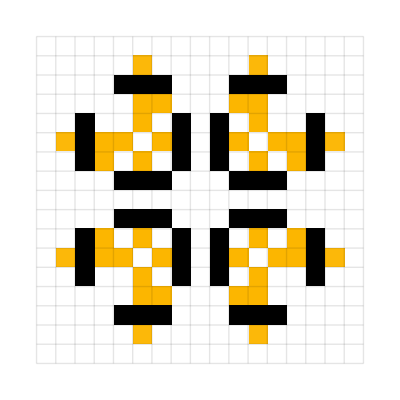
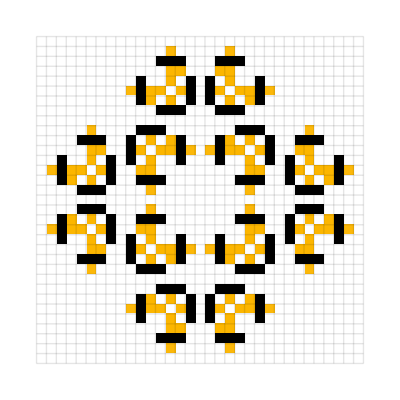
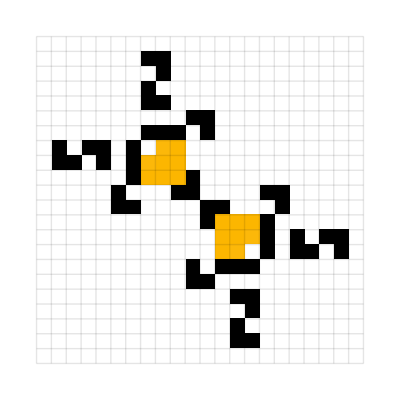
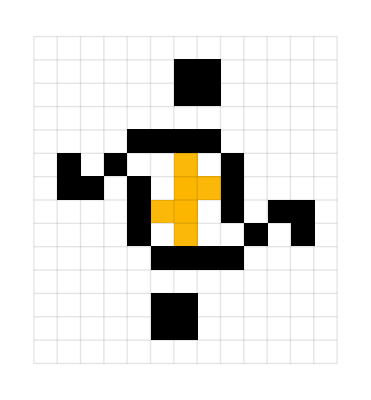
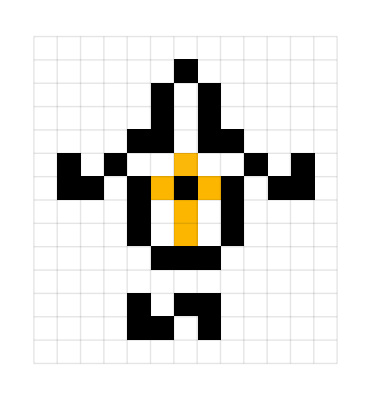
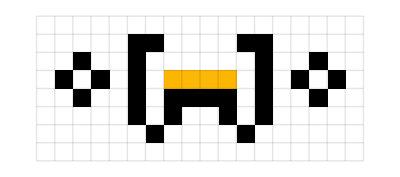
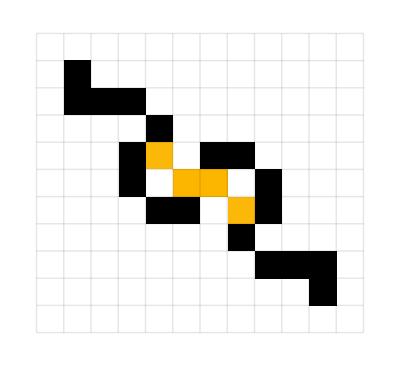
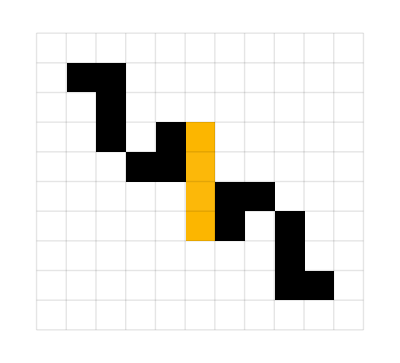
-Graphics-1970-Graphics-1970-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1973-Graphics-1973-Graphics-1973-Graphics-1977-Graphics-1982-Graphics-1985-Graphics-1988-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1990-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1994-Graphics-1997-Graphics-2003-Graphics-2012-Graphics-2017-Graphics-2018-Graphics-2021-Graphics-2022

```mathematica
With[{p3 = SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==3&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&]},
improvements = Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Infinity,p3]];
Row[Values[
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},6,MeshStyle->Opacity[.1],ImageSize->11 Sqrt[1+Last[Dimensions[#MatrixData]]], FrameStyle->If[MemberQ[improvements, #], Red, Automatic]],Text[Style[#Year,9,Gray]]]&/@p3],Spacer[1]]]
```

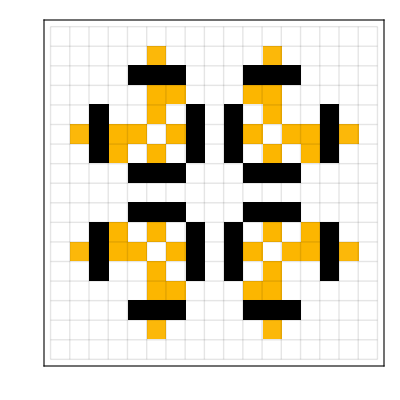
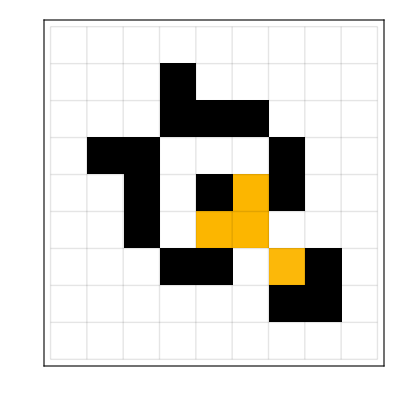
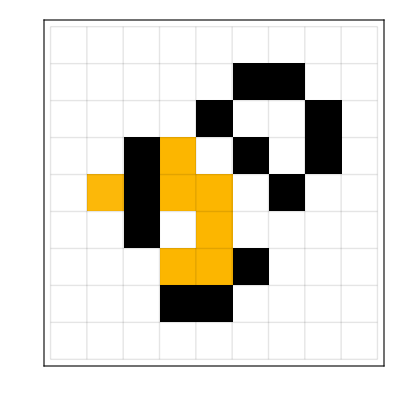
-Graphics-1970-Graphics-1970-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1973-Graphics-1973-Graphics-1973-Graphics-1977-Graphics-1982-Graphics-1985-Graphics-1988-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1990-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1994-Graphics-1997-Graphics-2003-Graphics-2012-Graphics-2017-Graphics-2018-Graphics-2021-Graphics-2022

```mathematica
Module[{p3 = SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==3&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&], improvements},
improvements = Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]];
Row[Values[
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},6,MeshStyle->Opacity[.1],ImageSize->11 Sqrt[1+Last[Dimensions[#MatrixData]]], Frame->MemberQ[improvements, #],FrameStyle->Directive[Red, Thickness[.05]]],Text[Style[#Year,9,Gray]]]&/@p3],Spacer[1]]]
```